```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Dropbox/PDF Euclidean Lattice/Hadron_Structure_Lattice/PDF/pion_PDF_HDF5

```mathematica
H=ConjugateTranspose;
```

```mathematica
{Nx,Ny,Nz,Nt}={4,4,4,32}
```

{4,4,4,32}

MmntmPrjctd[trcdprpgtr_,P_?((Head[#]==List)&&(Length[#]==3)&)]:=Table[ParallelSum[E^(-I*2π*(P⟦1⟧*i/Nx+P⟦2⟧*j/Ny+P⟦3⟧*k/Nz))*trcdprpgtr⟦i,j,k,t⟧,{i,Nx},{j,Ny},{k,Nz}],{t,Nt}]

The above is incorrect because the index of list starts from 0 in Mathematica, while Fourier starts from 0

```mathematica
MmntmPrjctd[trcdprpgtr_,P_?((Head[#]==List)&&(Length[#]==3)&)]:=Table[ParallelSum[E^(-I*2π*(P⟦1⟧*(i-1)/Nx+P⟦2⟧*(j-1)/Ny+P⟦3⟧*(k-1)/Nz))*trcdprpgtr⟦i,j,k,t⟧,{i,Nx},{j,Ny},{k,Nz}],{t,Nt}]
```

## quark propagator calculated from transformed gauge configuration, S_F[n_x,n_y,n_z,n_t] = (T_01^(a_n b_src) | ... | ... | T_03^(a_n b_src) ... | ... | ... | ... ... | ... | ... | ... T_31^(a_n b_src) | ... | ... | T_33^(a_n b_src)) is the propagator src→ LatticeSite [n_x,n_y,n_z,n_t], SFTrnsfmdF[{n_x,n_y,n_z,n_t}]⟦α,β⟧=T_αβ, T_αβ is an 3×3 SU(3) color matrix (α_n,β_src are Dirac Spinor indices and a,b are color indices)

## Before rgauge

### 1st propagator

```mathematica
qPrpgtr1stRe=Import["quark_prpgtr_1st.h5",{"Datasets","/Re"}];
```

```mathematica
qPrpgtr1stIm=Import["quark_prpgtr_1st.h5",{"Datasets","/Im"}];
```

```mathematica
qPrpgtr1st=qPrpgtr1stRe+I*qPrpgtr1stIm;
```

```mathematica
qPrpgtr1stLttcSpnClr=Transpose[ArrayReshape[qPrpgtr1st,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### shifted propagator

```mathematica
qPrpgtrshftdRe=Import["quark_prpgtr_shftd.h5",{"Datasets","/Re"}];
```

```mathematica
qPrpgtrshftdIm=Import["quark_prpgtr_shftd.h5",{"Datasets","/Im"}];
```

```mathematica
qPrpgtrshftd=qPrpgtrshftdRe+I*qPrpgtrshftdIm;
```

```mathematica
qPrpgtrshftdLttcSpnClr=Transpose[ArrayReshape[qPrpgtrshftd,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### gauge link

```mathematica
glinkRe=Import["gaugelink.h5",{"Datasets","/Re"}];
```

```mathematica
glinkIm=Import["gaugelink.h5",{"Datasets","/Im"}];
```

```mathematica
glink=Transpose[ArrayReshape[glinkRe+I*glinkIm,{32,4,4,4,3,3}],{4,3,2,1,5,6}];
```

### Feynman - Hellman source

```mathematica
FHqSrcRe=Import["FH_src.h5",{"Datasets","/Re"}];
```

```mathematica
FHqSrcIm=Import["FH_src.h5",{"Datasets","/Im"}];
```

```mathematica
FHqSrc=FHqSrcRe+I*FHqSrcIm;
```

```mathematica
FHqSrcLttcSpnClr=Transpose[ArrayReshape[FHqSrc,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### Feynman - Hellman propagator

```mathematica
FHqPrpgtrRe=Import["FH_quark_prpgtr.h5",{"Datasets","/Re"}];
```

```mathematica
FHqPrpgtrIm=Import["FH_quark_prpgtr.h5",{"Datasets","/Im"}];
```

```mathematica
FHqPrpgtr=FHqPrpgtrRe+I*FHqPrpgtrIm;
```

```mathematica
FHqPrpgtrLttcSpnClr=Transpose[ArrayReshape[FHqPrpgtr,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

## rgauge

```mathematica
grgaugeRe=Import["g_Re.h5",{"Datasets","/Re"}];
```

```mathematica
grgaugeIm=Import["g_Im.h5",{"Datasets","/Im"}];
```

```mathematica
grgauge=Transpose[ArrayReshape[grgaugeRe+I*grgaugeIm,{32,4,4,4,3,3}],{4,3,2,1,5,6}];
```

```mathematica
grgauge⟦1,2,1,13⟧//Det
```

1.+2.77556×10^-17 ⅈ

## After rgauge

### 1 st propagator

```mathematica
qPrpgtr1strgaugedRe=Import["quark_prpgtr_1st_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
qPrpgtr1strgaugedIm=Import["quark_prpgtr_1st_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
qPrpgtr1strgauged=qPrpgtr1strgaugedRe+I*qPrpgtr1strgaugedIm;
```

```mathematica
qPrpgtr1strgaugedLttcSpnClr=Transpose[ArrayReshape[qPrpgtr1strgauged,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### gauge link

```mathematica
glinkrgaugedRe=Import["gaugelink_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
glinkrgaugedIm=Import["gaugelink_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
glinkrgauged=Transpose[ArrayReshape[glinkrgaugedRe+I*glinkrgaugedIm,{32,4,4,4,3,3}],{4,3,2,1,5,6}];
```

### Feynman - Hellman source

```mathematica
FHqSrcrgaugedRe=Import["FH_src_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
FHqSrcrgaugedIm=Import["FH_src_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
FHqSrcrgauged=FHqSrcrgaugedRe+I*FHqSrcrgaugedIm;
```

```mathematica
FHqSrcrgaugedLttcSpnClr=Transpose[ArrayReshape[FHqSrcrgauged,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### Feynman - Hellman propagator

```mathematica
FHqPrpgtrrgaugedRe=Import["FH_quark_prpgtr_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
FHqPrpgtrrgaugedIm=Import["FH_quark_prpgtr_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
FHqPrpgtrrgauged=FHqPrpgtrrgaugedRe+I*FHqPrpgtrrgaugedIm;
```

```mathematica
FHqPrpgtrrgaugedLttcSpnClr=Transpose[ArrayReshape[FHqPrpgtrrgauged,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

## Checks

### Check gauge transformation on gaugelink

```mathematica
glink//Dimensions
```

{4,4,4,32,3,3}

```mathematica
glink⟦2,1,1,4⟧
```

### Check shifted quark propagator (checked)

```mathematica
qPrpgtr1stLttcSpnClr⟦1,1,2,1⟧
```

((-0.00311193-0.00103611 ⅈ | -0.00310027+0.0170559 ⅈ | -0.0182583-0.0150202 ⅈ
0.026704-0.0115207 ⅈ | 0.0034449-0.00333981 ⅈ | -0.00324864-0.00752629 ⅈ
0.00531481+0.000264242 ⅈ | -0.020374+0.00998498 ⅈ | -0.00276984+0.0152323 ⅈ) | (0.00213419+0.000854323 ⅈ | 0.000368527+0.000747022 ⅈ | -0.00080567+0.000774819 ⅈ
-0.000722586+0.000999245 ⅈ | -0.00215867+0.00032387 ⅈ | 0.000635547-0.00075363 ⅈ
-0.000257118+0.000227747 ⅈ | -0.000182712-0.00144144 ⅈ | 0.000823192-0.000198097 ⅈ) | (-0.00134209+0.000104177 ⅈ | -0.0188022-0.00302441 ⅈ | 0.0241904-0.0208491 ⅈ
0.011545+0.0340681 ⅈ | 0.00276797+0.00345144 ⅈ | 0.00182962+0.000512465 ⅈ
0.000112147+0.00641697 ⅈ | -0.0103534-0.0273288 ⅈ | -0.0183553-0.00529043 ⅈ) | (0.000292626-0.00066628 ⅈ | -0.00112302-0.00118948 ⅈ | 0.000329489-0.000237549 ⅈ
0.000713107+0.0000720051 ⅈ | -0.000109059-0.000191369 ⅈ | 0.000224735+0.000423239 ⅈ
0.0000674864+0.000517904 ⅈ | -0.000934949-0.000100512 ⅈ | -0.000639773+0.0000216222 ⅈ)
(0.000246824-0.000219263 ⅈ | 0.000440511+0.000953926 ⅈ | 0.00112151-0.00145264 ⅈ
0.00098113-0.000787919 ⅈ | -0.0000137965+0.000446682 ⅈ | -0.00123927+0.000184001 ⅈ
0.0017684-0.00113481 ⅈ | 0.000436294+0.000427107 ⅈ | 0.00134563-0.00122612 ⅈ) | (-0.00522162-0.0011854 ⅈ | -0.0035703+0.0156649 ⅈ | -0.0171837-0.0149762 ⅈ
0.0256108-0.0103594 ⅈ | 0.00303064-0.00265252 ⅈ | -0.00172005-0.00605767 ⅈ
0.00551422+0.000028506 ⅈ | -0.023187+0.0109841 ⅈ | -0.00330841+0.0155744 ⅈ) | (-0.000254236+0.00080107 ⅈ | -0.000184929+0.000209111 ⅈ | -0.000321252+0.000570033 ⅈ
0.000323736-0.00039358 ⅈ | -0.0000177182+0.000234893 ⅈ | 0.000554558-0.000918319 ⅈ
0.00048313-0.00015622 ⅈ | 0.000588599+0.000888273 ⅈ | -0.00118519+0.000673079 ⅈ) | (0.00116151-0.000638694 ⅈ | 0.0189401+0.00294441 ⅈ | -0.0230679+0.0207239 ⅈ
-0.0118264-0.034253 ⅈ | -0.00248589-0.00382664 ⅈ | -0.00265668-0.000177988 ⅈ
0.000202273-0.00605189 ⅈ | 0.0110227+0.0281189 ⅈ | 0.0183056+0.00553091 ⅈ)
(0.00104039-0.00115252 ⅈ | 0.0186555+0.00298484 ⅈ | -0.0232178+0.020737 ⅈ
-0.0118275-0.034468 ⅈ | -0.00220057-0.00364169 ⅈ | -0.00299707+0.000243272 ⅈ
-0.00030552-0.0062446 ⅈ | 0.0108223+0.0277212 ⅈ | 0.0182614+0.00547624 ⅈ) | (-0.000288752+0.000272227 ⅈ | 0.00105169+0.000958176 ⅈ | 0.0000784239+0.000214057 ⅈ
-0.000417243-0.000245521 ⅈ | 0.0003193+0.000239339 ⅈ | -0.000383793+0.00010232 ⅈ
-0.000159011-0.000439482 ⅈ | 0.000742773+0.000481582 ⅈ | 0.000904008-0.000662904 ⅈ) | (-0.00511717-0.000901477 ⅈ | -0.00360417+0.0158937 ⅈ | -0.0172861-0.0149466 ⅈ
0.0256606-0.010223 ⅈ | 0.00293805-0.00288154 ⅈ | -0.00193551-0.00630944 ⅈ
0.00544276+0.0000129281 ⅈ | -0.0230982+0.0106991 ⅈ | -0.00327442+0.0154295 ⅈ) | (0.00190986+0.000959091 ⅈ | -0.000137112+0.00067194 ⅈ | -0.00102135+0.000925585 ⅈ
-0.000634657+0.000944202 ⅈ | -0.00218699+0.000346368 ⅈ | 0.000517435-0.000715044 ⅈ
-0.000237363+0.000435757 ⅈ | -0.0000877946-0.0012597 ⅈ | 0.000417061-0.0000766139 ⅈ)
(0.000146214-0.000373388 ⅈ | 0.00029351+0.000276306 ⅈ | 0.000244601-0.0000754045 ⅈ
0.000184489+0.000755681 ⅈ | -0.0000256896-0.0005336 ⅈ | -0.000100142+0.000616684 ⅈ
-0.000470972+0.000640805 ⅈ | -0.0002848-0.000964019 ⅈ | 0.00102279-0.000591389 ⅈ) | (-0.00137302-0.000390197 ⅈ | -0.0190303-0.00292595 ⅈ | 0.0240481-0.0206957 ⅈ
0.0115262+0.0337868 ⅈ | 0.00293558+0.00347851 ⅈ | 0.00139465+0.000772893 ⅈ
-0.000346386+0.00636808 ⅈ | -0.0105412-0.0276741 ⅈ | -0.018459-0.00527957 ⅈ) | (0.000169725-0.00017549 ⅈ | -0.0000706994+0.00088608 ⅈ | 0.000880792-0.0012564 ⅈ
0.000958623-0.000861889 ⅈ | 0.000306031+0.000115874 ⅈ | -0.00105042+0.000177993 ⅈ
0.00172559-0.00100653 ⅈ | 0.000407763+0.000613082 ⅈ | 0.00114249-0.00138272 ⅈ) | (-0.00322194-0.00126733 ⅈ | -0.00291546+0.0168782 ⅈ | -0.0181567-0.0151046 ⅈ
0.0265352-0.0116674 ⅈ | 0.0034525-0.00309529 ⅈ | -0.00301782-0.00716188 ⅈ
0.00539133+0.000259982 ⅈ | -0.0204679+0.0103101 ⅈ | -0.00272723+0.0152936 ⅈ))

```mathematica
qPrpgtrshftdLttcSpnClr⟦1,1,1,1⟧
```

((-0.00311193-0.00103611 ⅈ | -0.00310027+0.0170559 ⅈ | -0.0182583-0.0150202 ⅈ
0.026704-0.0115207 ⅈ | 0.0034449-0.00333981 ⅈ | -0.00324864-0.00752629 ⅈ
0.00531481+0.000264242 ⅈ | -0.020374+0.00998498 ⅈ | -0.00276984+0.0152323 ⅈ) | (0.00213419+0.000854323 ⅈ | 0.000368527+0.000747022 ⅈ | -0.00080567+0.000774819 ⅈ
-0.000722586+0.000999245 ⅈ | -0.00215867+0.00032387 ⅈ | 0.000635547-0.00075363 ⅈ
-0.000257118+0.000227747 ⅈ | -0.000182712-0.00144144 ⅈ | 0.000823192-0.000198097 ⅈ) | (-0.00134209+0.000104177 ⅈ | -0.0188022-0.00302441 ⅈ | 0.0241904-0.0208491 ⅈ
0.011545+0.0340681 ⅈ | 0.00276797+0.00345144 ⅈ | 0.00182962+0.000512465 ⅈ
0.000112147+0.00641697 ⅈ | -0.0103534-0.0273288 ⅈ | -0.0183553-0.00529043 ⅈ) | (0.000292626-0.00066628 ⅈ | -0.00112302-0.00118948 ⅈ | 0.000329489-0.000237549 ⅈ
0.000713107+0.0000720051 ⅈ | -0.000109059-0.000191369 ⅈ | 0.000224735+0.000423239 ⅈ
0.0000674864+0.000517904 ⅈ | -0.000934949-0.000100512 ⅈ | -0.000639773+0.0000216222 ⅈ)
(0.000246824-0.000219263 ⅈ | 0.000440511+0.000953926 ⅈ | 0.00112151-0.00145264 ⅈ
0.00098113-0.000787919 ⅈ | -0.0000137965+0.000446682 ⅈ | -0.00123927+0.000184001 ⅈ
0.0017684-0.00113481 ⅈ | 0.000436294+0.000427107 ⅈ | 0.00134563-0.00122612 ⅈ) | (-0.00522162-0.0011854 ⅈ | -0.0035703+0.0156649 ⅈ | -0.0171837-0.0149762 ⅈ
0.0256108-0.0103594 ⅈ | 0.00303064-0.00265252 ⅈ | -0.00172005-0.00605767 ⅈ
0.00551422+0.000028506 ⅈ | -0.023187+0.0109841 ⅈ | -0.00330841+0.0155744 ⅈ) | (-0.000254236+0.00080107 ⅈ | -0.000184929+0.000209111 ⅈ | -0.000321252+0.000570033 ⅈ
0.000323736-0.00039358 ⅈ | -0.0000177182+0.000234893 ⅈ | 0.000554558-0.000918319 ⅈ
0.00048313-0.00015622 ⅈ | 0.000588599+0.000888273 ⅈ | -0.00118519+0.000673079 ⅈ) | (0.00116151-0.000638694 ⅈ | 0.0189401+0.00294441 ⅈ | -0.0230679+0.0207239 ⅈ
-0.0118264-0.034253 ⅈ | -0.00248589-0.00382664 ⅈ | -0.00265668-0.000177988 ⅈ
0.000202273-0.00605189 ⅈ | 0.0110227+0.0281189 ⅈ | 0.0183056+0.00553091 ⅈ)
(0.00104039-0.00115252 ⅈ | 0.0186555+0.00298484 ⅈ | -0.0232178+0.020737 ⅈ
-0.0118275-0.034468 ⅈ | -0.00220057-0.00364169 ⅈ | -0.00299707+0.000243272 ⅈ
-0.00030552-0.0062446 ⅈ | 0.0108223+0.0277212 ⅈ | 0.0182614+0.00547624 ⅈ) | (-0.000288752+0.000272227 ⅈ | 0.00105169+0.000958176 ⅈ | 0.0000784239+0.000214057 ⅈ
-0.000417243-0.000245521 ⅈ | 0.0003193+0.000239339 ⅈ | -0.000383793+0.00010232 ⅈ
-0.000159011-0.000439482 ⅈ | 0.000742773+0.000481582 ⅈ | 0.000904008-0.000662904 ⅈ) | (-0.00511717-0.000901477 ⅈ | -0.00360417+0.0158937 ⅈ | -0.0172861-0.0149466 ⅈ
0.0256606-0.010223 ⅈ | 0.00293805-0.00288154 ⅈ | -0.00193551-0.00630944 ⅈ
0.00544276+0.0000129281 ⅈ | -0.0230982+0.0106991 ⅈ | -0.00327442+0.0154295 ⅈ) | (0.00190986+0.000959091 ⅈ | -0.000137112+0.00067194 ⅈ | -0.00102135+0.000925585 ⅈ
-0.000634657+0.000944202 ⅈ | -0.00218699+0.000346368 ⅈ | 0.000517435-0.000715044 ⅈ
-0.000237363+0.000435757 ⅈ | -0.0000877946-0.0012597 ⅈ | 0.000417061-0.0000766139 ⅈ)
(0.000146214-0.000373388 ⅈ | 0.00029351+0.000276306 ⅈ | 0.000244601-0.0000754045 ⅈ
0.000184489+0.000755681 ⅈ | -0.0000256896-0.0005336 ⅈ | -0.000100142+0.000616684 ⅈ
-0.000470972+0.000640805 ⅈ | -0.0002848-0.000964019 ⅈ | 0.00102279-0.000591389 ⅈ) | (-0.00137302-0.000390197 ⅈ | -0.0190303-0.00292595 ⅈ | 0.0240481-0.0206957 ⅈ
0.0115262+0.0337868 ⅈ | 0.00293558+0.00347851 ⅈ | 0.00139465+0.000772893 ⅈ
-0.000346386+0.00636808 ⅈ | -0.0105412-0.0276741 ⅈ | -0.018459-0.00527957 ⅈ) | (0.000169725-0.00017549 ⅈ | -0.0000706994+0.00088608 ⅈ | 0.000880792-0.0012564 ⅈ
0.000958623-0.000861889 ⅈ | 0.000306031+0.000115874 ⅈ | -0.00105042+0.000177993 ⅈ
0.00172559-0.00100653 ⅈ | 0.000407763+0.000613082 ⅈ | 0.00114249-0.00138272 ⅈ) | (-0.00322194-0.00126733 ⅈ | -0.00291546+0.0168782 ⅈ | -0.0181567-0.0151046 ⅈ
0.0265352-0.0116674 ⅈ | 0.0034525-0.00309529 ⅈ | -0.00301782-0.00716188 ⅈ
0.00539133+0.000259982 ⅈ | -0.0204679+0.0103101 ⅈ | -0.00272723+0.0152936 ⅈ))

### Check Feynman-Hellman source Src^FH[n]=W[n,n+Δz]*S[n+Δz←src] (checked)

```mathematica
γz=({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}});
```

```mathematica
FHSrcMMA=Table[Sum[γz⟦i,j⟧*qPrpgtr1stLttcSpnClr⟦1,1,2,1⟧⟦j,k⟧,{j,1,4}],{i,1,4},{k,1,4}];
```

```mathematica
glink⟦1,1,1,1⟧.FHSrcMMA⟦1,1⟧
```

(0.00113478-0.036739 ⅈ | 0.000657461+0.00109643 ⅈ | 0.00289519-0.00125726 ⅈ
-0.00086163-0.000823575 ⅈ | 0.000652182-0.0354475 ⅈ | 0.0013726+0.00109185 ⅈ
0.00260389+0.00319179 ⅈ | 0.00134979-0.000472244 ⅈ | 0.00298938-0.0363266 ⅈ)

```mathematica
FHqSrcLttcSpnClr⟦1,1,1,1⟧⟦1,1⟧
```

(0.00113478-0.036739 ⅈ | 0.000657461+0.00109643 ⅈ | 0.00289519-0.00125726 ⅈ
-0.00086163-0.000823575 ⅈ | 0.000652182-0.0354475 ⅈ | 0.0013726+0.00109185 ⅈ
0.00260389+0.00319179 ⅈ | 0.00134979-0.000472244 ⅈ | 0.00298938-0.0363266 ⅈ)

```mathematica
glink⟦1,1,1,1⟧.FHSrcMMA⟦2,2⟧
```

(-0.00129213+0.0361619 ⅈ | 0.000154874-0.000981472 ⅈ | -0.00480753+0.00165065 ⅈ
0.000577677+0.00115291 ⅈ | -0.000679895+0.0355735 ⅈ | -0.00149259-0.00166488 ⅈ
-0.0012673-0.00211833 ⅈ | -0.00120306+0.000187914 ⅈ | -0.00339915+0.0365429 ⅈ)

```mathematica
FHqSrcLttcSpnClr⟦1,1,1,1⟧⟦2,2⟧
```

(-0.00129213+0.0361619 ⅈ | 0.000154874-0.000981472 ⅈ | -0.00480753+0.00165065 ⅈ
0.000577677+0.00115291 ⅈ | -0.000679895+0.0355735 ⅈ | -0.00149259-0.00166488 ⅈ
-0.0012673-0.00211833 ⅈ | -0.00120306+0.000187914 ⅈ | -0.00339915+0.0365429 ⅈ)

### Check Feynman-Hellman propagator S^FH[n← src]=W[n,n+Δz]*S[n+Δz←src]

```mathematica
FHqPrpgtrLttcSpnClr⟦1,1,1,1⟧⟦1,1⟧
```

(-0.00054008+0.000496182 ⅈ | -0.0000121068+0.000143335 ⅈ | 0.000430024+0.0000376376 ⅈ
0.000269698-0.0000217724 ⅈ | 0.000243554+0.00121889 ⅈ | -0.000158169-0.000658451 ⅈ
0.000604123+0.000370811 ⅈ | 0.0000840573-0.00061186 ⅈ | 0.000243302+0.000540869 ⅈ)

### Check gauge transformation on propagator

```mathematica
grgauge⟦2,1,3,2⟧.qPrpgtr1stLttcSpnClr⟦2,1,3,2,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(-0.0000201784+0.00036995 ⅈ | 0.000187757-0.0000170413 ⅈ | -3.13711×10^-6-0.00107393 ⅈ
-0.000175147-0.0000101412 ⅈ | -0.000135257-0.000148053 ⅈ | -0.000976933+0.000500668 ⅈ
-0.00144519+0.0000194766 ⅈ | 0.000742223-0.00037353 ⅈ | -0.000829777-0.000211621 ⅈ)

```mathematica
qPrpgtr1strgaugedLttcSpnClr⟦2,1,3,2,1,1⟧
```

(-0.0000201784+0.00036995 ⅈ | 0.000187757-0.0000170413 ⅈ | -3.13711×10^-6-0.00107393 ⅈ
-0.000175147-0.0000101412 ⅈ | -0.000135257-0.000148053 ⅈ | -0.000976933+0.000500668 ⅈ
-0.00144519+0.0000194766 ⅈ | 0.000742223-0.00037353 ⅈ | -0.000829777-0.000211621 ⅈ)

```mathematica
grgauge⟦1,1,1,4⟧.qPrpgtr1stLttcSpnClr⟦1,1,1,4,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

```mathematica
qPrpgtr1strgaugedLttcSpnClr⟦1,1,1,4,1,1⟧
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

```mathematica
ArrayReshape[{1,I}.#&/@ToExpression[StringReplace["{{0.249036,-2.76181e-19},{0.000340879,8.65219e-05},{0.00133894,-0.000478686},{0.000340879,-8.65219e-05},{0.248141,-1.54661e-18},{0.000897637,0.000133951},{0.00133894,0.000478686},{0.000897637,-0.000133951},{0.247288,3.14846e-18}}","e"->"*^"]],{3,3}]
```

(0.249036-2.76181×10^-19 ⅈ | 0.000340879+0.0000865219 ⅈ | 0.00133894-0.000478686 ⅈ
0.000340879-0.0000865219 ⅈ | 0.248141-1.54661×10^-18 ⅈ | 0.000897637+0.000133951 ⅈ
0.00133894+0.000478686 ⅈ | 0.000897637-0.000133951 ⅈ | 0.247288+3.14846×10^-18 ⅈ)

```mathematica
NumberForm[qPrpgtr1stLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

(0.249036-(6.07597×10^-19) ⅈ | 0.000340879+0.0000865219 ⅈ | 0.00133894-0.000478686 ⅈ
0.000340879-0.0000865219 ⅈ | 0.248141-(6.90451×10^-19) ⅈ | 0.000897637+0.000133951 ⅈ
0.00133894+0.000478686 ⅈ | 0.000897637-0.000133951 ⅈ | 0.247288+(2.54086×10^-18) ⅈ)

```mathematica
NumberForm[FHqSrcLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

(0.000235287-0.000275779 ⅈ | 0.0000543657+0.000057928 ⅈ | 0.000158065-0.0000296877 ⅈ
-0.0000303011+0.000113184 ⅈ | 0.000117111-0.000148606 ⅈ | 0.0000969412-0.0000400537 ⅈ
0.000131583+0.0000673195 ⅈ | 0.0000193588+0.000038264 ⅈ | 0.000175657-0.000178212 ⅈ)

```mathematica
NumberForm[FHqPrpgtrLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

(-2.22534×10^-6+(6.95247×10^-6) ⅈ | 6.02254×10^-6+0.0000526522 ⅈ | 0.0000247701+(1.54955×10^-6) ⅈ
-0.000010343+0.00004973 ⅈ | -7.22998×10^-6+0.0000513585 ⅈ | 0.0000182243-0.0000342421 ⅈ
-0.0000215432+0.0000508658 ⅈ | -0.0000157803-0.0000244807 ⅈ | 0.0000177674+0.0000446142 ⅈ)

```mathematica
NumberForm[FHqPrpgtrLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

```mathematica
grgauge⟦1,1,1,4⟧.qPrpgtr1stLttcSpnClr⟦1,1,1,4,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

```mathematica
qPrpgtr1strgaugedLttcSpnClr⟦1,1,1,4,1,1⟧
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

### Check gauge transformation on Feynman-Hellman source

```mathematica
grgauge⟦1,1,1,4⟧.FHqSrcLttcSpnClr⟦1,1,1,4,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(-0.0000707417+6.92052×10^-7 ⅈ | 0.0000178532+0.0000355655 ⅈ | 0.0000194635+0.0000430777 ⅈ
8.68589×10^-6-0.0000405943 ⅈ | -0.0000202048-3.77592×10^-6 ⅈ | -0.0000153076+3.95191×10^-6 ⅈ
-4.34355×10^-6-0.0000116199 ⅈ | 0.0000175858+0.0000151519 ⅈ | 4.26021×10^-6+7.12632×10^-6 ⅈ)

```mathematica
FHqSrcrgaugedLttcSpnClr⟦1,1,1,4,1,1⟧
```

(-0.0000707417+6.92052×10^-7 ⅈ | 0.0000178532+0.0000355655 ⅈ | 0.0000194635+0.0000430777 ⅈ
8.68589×10^-6-0.0000405943 ⅈ | -0.0000202048-3.77592×10^-6 ⅈ | -0.0000153076+3.95191×10^-6 ⅈ
-4.34355×10^-6-0.0000116199 ⅈ | 0.0000175858+0.0000151519 ⅈ | 4.26021×10^-6+7.12632×10^-6 ⅈ)

```mathematica
<<XML`
```

```mathematica
<<MaTeX`
```

```mathematica
FP0zXMLdat=StringReplace[Import["pion_correlator"],{"\n"->"","<?xml version="~~x__~~"?>"->"","<PseudoScalar>"->"","</PseudoScalar>"->""}];
```

```mathematica
FP0ztdat=Flatten[(ImportString[FP0zXMLdat,"XML"]//.{XMLElement["re",{},{x__}],XMLElement["im",{},{y__}]}:>ToExpression[StringReplace[x,"e"->"*^"]]+I*ToExpression[StringReplace[y,"e"->"*^"]]//.{XMLElement["elem",{},y_]->y,XMLElement["OLattice",{},y_]->y})⟦2,-1,-1⟧];
```

```mathematica
Evan=ToExpression[StringReplace["{1.50939502e-04 -2.58204955e-04j  -5.81637563e-03 -3.52101910e-03j
  -1.21073366e-03 -6.87272967e-04j  -2.71334016e-04 -1.48938480e-04j
  -5.79560168e-05 -3.41965357e-05j  -1.02351854e-05 -6.43287815e-06j
  -1.77255727e-06 -1.19330009e-06j  -2.98680914e-07 -1.89073570e-07j
  -5.01602706e-08 -2.85732100e-08j  -8.81932028e-09 -4.79817074e-09j
  -1.41277945e-09 -8.16297376e-10j  -2.11389816e-10 -1.18125749e-10j
  -3.39281133e-11 -1.53052013e-11j  -5.18230633e-12 -1.68033333e-12j
  -7.77856966e-13 -1.63106358e-13j  -1.18939563e-13 -1.06460281e-14j
   1.12314582e-14 +8.97112107e-15j   1.44126225e-13 +6.24711019e-14j
   9.16956420e-13 +5.06801541e-13j   5.51644469e-12 +3.75878201e-12j
   3.17148874e-11 +2.45794761e-11j   1.81779335e-10 +1.48731611e-10j
   1.10268468e-09 +9.23332231e-10j   5.61570323e-09 +5.15001481e-09j
   3.05195710e-08 +2.99057365e-08j   2.05079462e-07 +1.83756788e-07j
   1.30766785e-06 +1.09783959e-06j   8.37705667e-06 +6.26008976e-06j
   5.56174177e-05 +3.80014259e-05j   3.90689010e-04 +2.50215728e-04j
   2.11481576e-03 +1.28653817e-03j   7.97392300e-03 +4.57969754e-03j}",{"e"->"*^","  "->","}]]//.j->I;
```

```mathematica
ReEvan=ListPlot[Evan//Re,PlotStyle->Red,PlotLegends->{"Evan, Re"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ReXng=ListPlot[-FP0ztdat//Re,PlotStyle->{Dashed,Black},Joined->True,PlotLegends->{"Xiong, Re"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ImEvan=ListPlot[Evan//Im,PlotStyle->Green,PlotLegends->{"Evan, Im"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ImXng=ListPlot[-FP0ztdat//Im,PlotStyle->{Dashed,Blue},Joined->True,PlotLegends->{"Xiong, Im"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsReEvan=ListPlot[Evan//Re//Abs//Log,PlotStyle->Red,PlotLegends->{"Evan, Log[Abs[Re[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsReXng=ListPlot[-FP0ztdat//Re//Abs//Log,PlotStyle->{Dashed,Black},Joined->True,PlotLegends->{"Xiong, Log[Abs[Re[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsImEvan=ListPlot[Evan//Im//Abs//Log,PlotStyle->Green,PlotLegends->{"Evan, Log[Abs[Im[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsImXng=ListPlot[-FP0ztdat//Im//Abs//Log,PlotStyle->{Dashed,Blue},Joined->True,PlotLegends->{"Xiong, Log[Abs[Im[]]]"},PlotRange->All,Frame->True,Axes->False];
```

Show

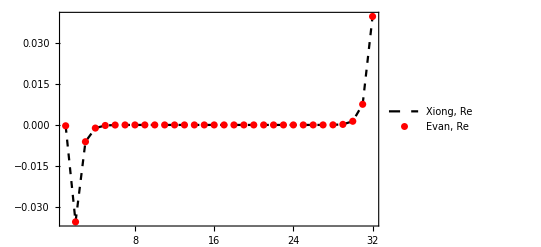
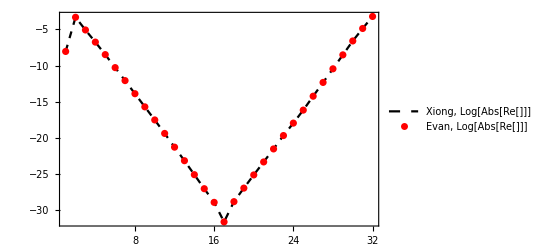
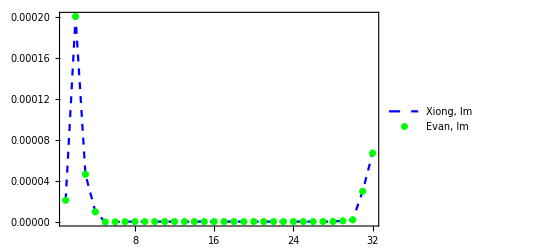
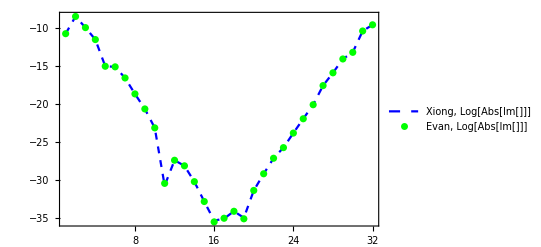
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_x\\langle\\pi^+(t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x]\\psi(x)\\right|\\pi^+(0)\\rangle}",Magnification->1.75],Top]
```

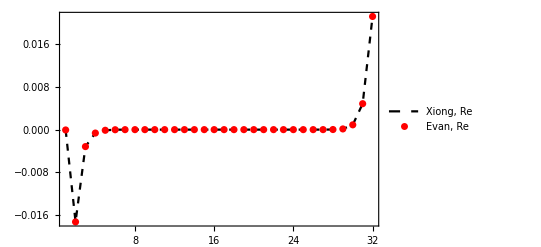
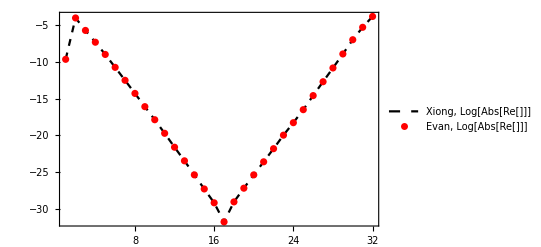
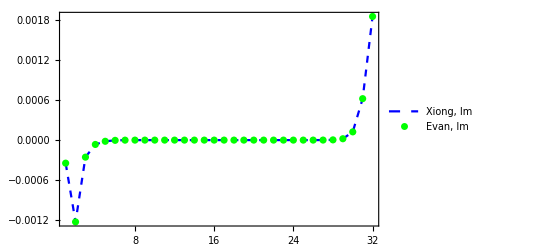
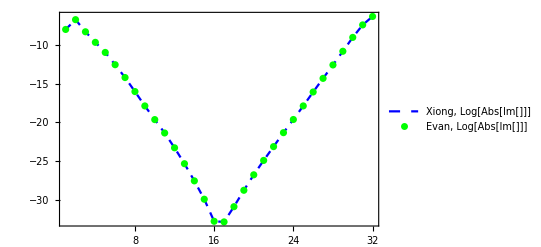
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_x\\langle\\pi^+(t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x-\\hat{z}]\\psi(x-\\hat{z})\\right|\\pi^+(0)\\rangle}",Magnification->1.75],Top]
```

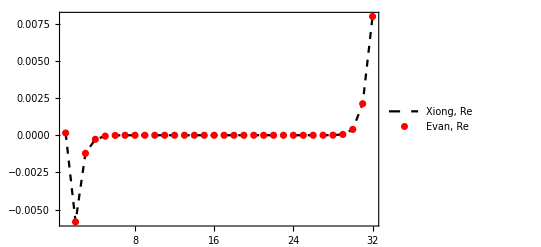
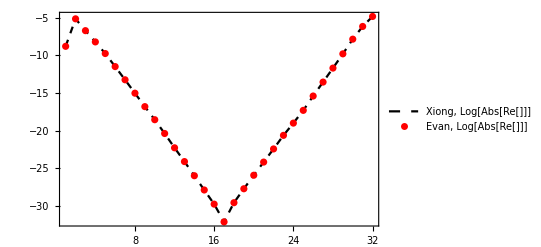
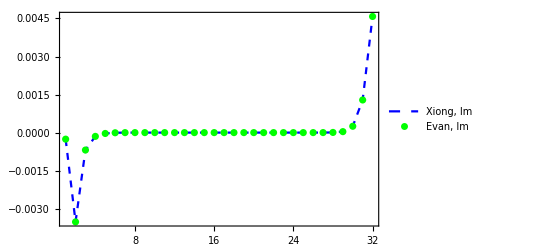
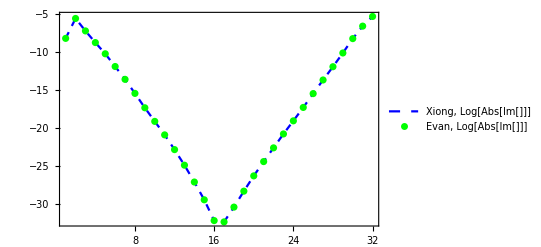
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

(1)⟦1,2,1,23⟧
 |  |  |  |

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_x\\langle\\pi^+(t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x-2\\hat{z}]\\psi(x-2\\hat{z})\\right|\\pi^+(0)\\rangle}",Magnification->1.75],Top]
```

### Check multi_shift boundary condition

```mathematica
Import["pion_PDF.h5"]
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>/ ,/FH_quark_prpgtr.h5/Im,/FH_quark_prpgtr.h5/Re,/FH_src.h5/Im,/FH_src.h5/Re,/gauge_link/Im,/gauge_link/Re,/quark_prpgtrs/Im,/quark_prpgtrs/Re,/quark_shftd_prpgtrs/Im,/quark_shftd_prpgtrs/Re,/tr_prpgtrs.h5/Im,/tr_prpgtrs.h5/Re}

```mathematica
Import["multi_shift.h5"]
```

{/coord_in_dir,/shft_phs_in_dir,/shftd_coord_in_dir}

```mathematica
LttcCrdnt=Transpose[Import["multi_shift.h5",{"Datasets","/coord_in_dir"}],{4,3,2,1}];
```

```mathematica
LttcShftdCrdnt=Transpose[Import["multi_shift.h5",{"Datasets","/shftd_coord_in_dir"}],{4,3,2,1}];
```

```mathematica
LttcShftPhs=Transpose[Import["multi_shift.h5",{"Datasets","/shft_phs_in_dir"}],{4,3,2,1}];
```

```mathematica
LttcShftPhs
```

((-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)
(-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)
(-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)
(-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.))

```mathematica
Clear[qPrpgtrReIm,qShftdPrpgtrReIm,qPrpgtr,qShftdPrpgtr]
```

```mathematica
qPrpgtrReIm=Import["pion_PDF.h5",{"Datasets","/quark_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets","/quark_prpgtrs/Im"}];
```

```mathematica
qShftdPrpgtrReIm=Import["pion_PDF.h5",{"Datasets","/quark_shftd_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets","/quark_shftd_prpgtrs/Im"}];
```

```mathematica
qPrpgtr=Transpose[ArrayReshape[qPrpgtrReIm,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

```mathematica
qShftdPrpgtr=Transpose[ArrayReshape[qShftdPrpgtrReIm,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

```mathematica
Chop[qPrpgtr⟦2,2,1,5,2,4⟧.Inverse[qShftdPrpgtr⟦2,2,1,3,2,4⟧],10^-8]
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

```mathematica
Chop[qPrpgtr⟦2,3,2,1,1,3⟧.Inverse[qShftdPrpgtr⟦2,3,2,31,1,3⟧],10^-8]
```

(-1. | 0 | 0
0 | -1. | 0
0 | 0 | -1.)

```mathematica
Chop[qPrpgtr⟦2,3,1,2,2,3⟧.Inverse[qShftdPrpgtr⟦2,3,1,32,2,3⟧],10^-8]
```

(-1. | 0 | 0
0 | -1. | 0
0 | 0 | -1.)

## correlation function Σ_x⟨π^+(t)|q̄(x)γ_z W[x,x+Δ_z]q(x+Δ_z)|π^+(0)⟩ , traced propagators

```mathematica
TagF[stp_,dir_]:="/<pi(y,t)|q-bar(x).ga_3.W[x,x+"<>ToString[stp]<>"_stps_in_"<>ToString[dir]<>"].q(x+"<>ToString[stp]<>"_stps_in_"<>ToString[dir]<>")|pi(0,0)>"
```

```mathematica
PDFtags=StringReplace[Import["pion_PDF.h5",{"Groups"}],"/<"~~X__~~">"~~Y__:>"/<"~~X~~">"]//Union
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_3].q(x+1_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+3_stps_in_3].q(x+3_stps_in_3)|pi(0,0)>}

```mathematica
TagF[2,2]
```

/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>

### -2 steps in dir_2

```mathematica
PDFtags=StringReplace[Import["pion_PDF.h5",{"Groups"}],"/<"~~X__~~">"~~Y__:>"/<"~~X~~">"]//Union
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>}

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[TagF[-2,2]];
```

```mathematica
{Nx,Ny,Nz,Nt}=Dimensions[trPrpgtrs]
```

{4,4,4,32}

```mathematica
Evan0Pz=ToExpression[StringReplace["[1.50939502e-04 -2.58204955e-04j  -5.81637563e-03 -3.52101910e-03j
  -1.21073366e-03 -6.87272967e-04j  -2.71334016e-04 -1.48938480e-04j
  -5.79560168e-05 -3.41965357e-05j  -1.02351854e-05 -6.43287815e-06j
  -1.77255727e-06 -1.19330009e-06j  -2.98680914e-07 -1.89073570e-07j
  -5.01602706e-08 -2.85732100e-08j  -8.81932028e-09 -4.79817074e-09j
  -1.41277945e-09 -8.16297377e-10j  -2.11389816e-10 -1.18125750e-10j
  -3.39281134e-11 -1.53052014e-11j  -5.18230635e-12 -1.68033333e-12j
  -7.77856964e-13 -1.63106354e-13j  -1.18939561e-13 -1.06460279e-14j
   1.12314577e-14 +8.97112009e-15j   1.44126222e-13 +6.24711003e-14j
   9.16956416e-13 +5.06801541e-13j   5.51644467e-12 +3.75878202e-12j
   3.17148874e-11 +2.45794762e-11j   1.81779335e-10 +1.48731611e-10j
   1.10268468e-09 +9.23332231e-10j   5.61570323e-09 +5.15001481e-09j
   3.05195710e-08 +2.99057365e-08j   2.05079463e-07 +1.83756788e-07j
   1.30766785e-06 +1.09783959e-06j   8.37705667e-06 +6.26008976e-06j
   5.56174177e-05 +3.80014259e-05j   3.90689010e-04 +2.50215728e-04j
   2.11481576e-03 +1.28653817e-03j   7.97392300e-03 +4.57969754e-03j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000154124 ⅈ,0.-0.0000304785 ⅈ,-0.0000102283-0.0000287086 ⅈ,-0.000405324+0.000136864 ⅈ,-0.0000815349+0.0000190122 ⅈ,-0.0000293803,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[-1.02985814e-04 +1.44262529e-04j  -1.87677684e-03 -1.04485134e-03j
  -3.06382668e-04 -1.45882475e-04j  -4.08867034e-05 -2.70715745e-05j
  -6.56182730e-06 -4.32378965e-06j  -7.51082848e-07 -5.09306053e-07j
  -2.19341071e-08 +6.04844804e-09j  -4.93523333e-09 -1.39422100e-09j
  -1.63333173e-09 -1.32578574e-09j  -1.50509786e-10 -1.45249134e-10j
  -6.22503335e-11 -5.39079043e-11j  -9.84399400e-12 -1.31644432e-11j
  -1.82801739e-12 -2.23955215e-12j  -1.74979543e-13 -2.40323006e-13j
  -3.76895450e-14 -3.01230049e-14j  -6.36095257e-15 -3.28649127e-15j
   2.28437334e-16 -4.71538503e-16j   3.80225390e-15 -1.28323757e-15j
   3.18997453e-14 -3.31951824e-15j   1.34017971e-13 -8.05233445e-14j
   2.79408755e-13 -1.08322541e-12j  -2.97894587e-13 -4.02027609e-12j
  -9.11928400e-12 -8.91340193e-12j  -3.17084648e-11 +2.22809665e-11j
  -9.65932230e-11 +8.44727795e-10j   1.80999550e-09 +3.68445863e-09j
   5.43254908e-08 +4.83009433e-08j   4.42315068e-07 +3.32556121e-07j
   4.55996068e-06 +2.78699293e-06j   3.49881577e-05 +2.93136808e-05j
   3.37146340e-04 +2.17108992e-04j   2.22603075e-03 +1.42853548e-03j]
",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz-1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000302303 ⅈ,0.0000184316-0.000039817 ⅈ,0.000128276+0.0000648722 ⅈ,0.000458143-0.000623251 ⅈ,-0.0000456149+0.000104867 ⅈ,0.000054415+0.0000262078 ⅈ,0.+0.0000194968 ⅈ,0.+0.0000127423 ⅈ,0,-0.0000119677,0.-0.0000130615 ⅈ,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### -1 steps in dir_2

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦2⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[-6.28627834e-05 -3.44672797e-04j  -1.73131373e-02 -1.22271710e-03j
  -3.18309328e-03 -2.54793178e-04j  -6.41919212e-04 -6.49597283e-05j
  -1.21959627e-04 -1.76167177e-05j  -2.11142435e-05 -3.60317888e-06j
  -3.62578748e-06 -6.84849743e-07j  -6.11177301e-07 -1.11714556e-07j
  -1.01298712e-07 -1.74197931e-08j  -1.71445482e-08 -2.97261031e-09j
  -2.70808286e-09 -5.25874855e-10j  -4.09533154e-10 -7.73861997e-11j
  -6.45165994e-11 -9.91545324e-12j  -9.58397294e-12 -1.07666840e-12j
  -1.41027807e-12 -1.00157210e-13j  -2.14933407e-13 -5.77208027e-15j
   1.60728432e-14 +5.33274005e-15j   2.43853781e-13 +3.81121451e-14j
   1.56655579e-12 +3.18837925e-13j   9.56007391e-12 +2.35739233e-12j
   5.64859545e-11 +1.51569401e-11j   3.35745348e-10 +9.02016615e-11j
   2.10522139e-09 +5.48953492e-10j   1.14789261e-08 +3.00736828e-09j
   6.72204439e-08 +1.74521794e-08j   4.54864065e-07 +1.05775484e-07j
   2.99525921e-06 +6.15862681e-07j   1.94129168e-05 +3.49180396e-06j
   1.30165754e-04 +2.04944769e-05j   8.99915191e-04 +1.23065334e-04j
   4.86687006e-03 +6.19602386e-04j   2.12352743e-02 +1.84846615e-03j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000134317 ⅈ,0.-0.0000298894 ⅈ,0.-0.0000361287 ⅈ,-0.000503949+0.0000989505 ⅈ,-0.0000714284+0.0000136856 ⅈ,-0.0000257257,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[-3.68596828e-04 +1.86378942e-04j  -4.53507551e-03 -1.23688114e-04j
  -7.15691327e-04 -5.19854334e-05j  -1.06212045e-04 -9.77980529e-06j
  -1.43916363e-05 -2.44094582e-06j  -1.62872953e-06 -3.52847608e-07j
  -7.06193009e-08 +1.63457725e-08j  -1.62888805e-08 +2.22386367e-09j
  -3.90152934e-09 -2.54749480e-10j  -3.17087160e-10 -1.43492262e-11j
  -1.39933388e-10 -3.63081898e-11j  -2.22577897e-11 -9.02313483e-12j
  -3.96881677e-12 -1.61209346e-12j  -4.28158385e-13 -1.92868541e-13j
  -7.50085969e-14 -2.68858439e-14j  -1.12051335e-14 -2.48965819e-15j
   6.11458990e-17 -5.31637495e-16j   4.79004851e-15 -1.63609782e-15j
   4.08024043e-14 -4.85925515e-15j   1.56399615e-13 -2.31275195e-14j
   6.08174895e-14 -3.72181717e-13j   3.07227671e-13 -1.67635744e-12j
  -9.32103578e-12 -3.76796975e-12j  -5.56829877e-11 -1.28642668e-11j
   4.54441703e-10 +6.46893494e-10j   2.25566302e-09 +2.59217104e-09j
   9.10007481e-08 +2.73546686e-08j   6.93022368e-07 +1.33855684e-07j
   7.60714431e-06 -1.02759417e-07j   5.24460285e-05 -9.36849771e-07j
   4.25405114e-04 +4.28262323e-05j   4.36271632e-03 +3.21914618e-04j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz-1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000190866-0.0000239499 ⅈ,0.000024905-0.0000300026 ⅈ,0.0000894323+0.0000827611 ⅈ,0.000694986-0.000809556 ⅈ,-0.0000719451+0.000144006 ⅈ,0.0000455875+0.0000157564 ⅈ,0.0000130841,0.0000235784+0.0000401833 ⅈ,0,-0.0000141734,-0.0000127016,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### 0 steps in dir_2

```mathematica
PDFtags
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>}

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦1⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[-3.16149391e-04 +2.07870543e-05j  -3.54263781e-02 +2.00178750e-04j
  -6.13424883e-03 +4.61609672e-05j  -1.15070267e-03 +9.57294632e-06j
  -2.04409336e-04 -2.85428333e-07j  -3.39576973e-05 -2.64287285e-07j
  -5.65596968e-06 -6.11627797e-08j  -9.26562301e-07 -7.51179604e-09j
  -1.50479520e-07 -1.03793954e-09j  -2.47200637e-08 -8.60764498e-11j
  -3.83728822e-09 +5.77784158e-14j  -5.76831127e-10 +1.21361221e-12j
  -8.89789269e-11 +5.83012126e-13j  -1.29343959e-11 +7.25542069e-14j
  -1.86639698e-12 +5.31736175e-15j  -2.82484281e-13 +3.63877498e-16j
   1.90734802e-14 -5.87065677e-16j   3.12352062e-13 -1.47093823e-15j
   2.02426202e-12 -5.47390328e-16j   1.24819661e-11 +2.28221419e-14j
   7.50100474e-11 +2.04592043e-13j   4.52308515e-10 +1.57981458e-12j
   2.86942848e-09 +6.38326558e-12j   1.59854565e-08 +4.34109443e-11j
   9.60952003e-08 +2.85179643e-10j   6.55686269e-07 +1.80970756e-09j
   4.38869420e-06 +2.24000271e-08j   2.87857714e-05 +1.20452017e-07j
   1.97219494e-04 +7.44812291e-07j   1.34744077e-03 +1.78435852e-06j
   7.54022817e-03 +2.95531501e-05j   3.96294987e-02 +6.67963960e-05j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000116384 ⅈ,0.-0.0000282237 ⅈ,0.-0.0000389938 ⅈ,-0.000533791,-0.0000639475+0.0000154325 ⅈ,-0.0000239328,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[-4.67258936e-04 +2.71189087e-05j  -2.12073771e-02 +5.80375694e-05j
  -2.65996816e-03 -3.84895227e-06j  -3.53512838e-04 +7.80264648e-07j
  -4.34159933e-05 -3.80345557e-07j  -4.70564968e-06 -1.02209459e-07j
  -3.30197048e-07 -3.64068545e-09j  -4.53354211e-08 +8.44582540e-10j
  -7.50185458e-09 +1.96627155e-10j  -5.96726716e-10 +3.89343104e-12j
  -2.33228698e-10 -1.31387015e-11j  -3.57817259e-11 -2.68504660e-12j
  -6.53211299e-12 -4.26597495e-13j  -7.88816629e-13 -4.27504278e-14j
  -1.28575434e-13 -5.83425979e-15j  -1.95187263e-14 -1.90874554e-16j
  -6.76078916e-16 -3.58567708e-16j   4.90875582e-15 -1.38394823e-15j
   4.34950432e-14 -5.78814582e-15j   1.27684076e-13 -2.35109091e-14j
  -3.94519785e-13 -6.50212207e-14j   1.29570866e-12 -1.01375699e-13j
   1.00250029e-11 +2.16348363e-12j   2.34125611e-10 +1.23323482e-11j
   3.57607230e-09 +2.98472397e-10j   2.80288886e-08 +1.33139342e-09j
   3.85621421e-07 +1.39398447e-08j   3.52745664e-06 +9.36549231e-08j
   3.55120931e-05 -2.69136346e-07j   3.24043706e-04 -4.32450168e-06j
   2.62833978e-03 +1.15940700e-05j   2.24359452e-02 +6.63033712e-05j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz-1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000182539-0.0000104942 ⅈ,0.0000307442-0.000023458 ⅈ,0.0000701998+0.000045266 ⅈ,0.000852984-0.0000498974 ⅈ,-0.000113676+0.000223615 ⅈ,0.0000346463+0.0000251774 ⅈ,0,-0.0000311295+0.0000311738 ⅈ,0,0.000025161,0,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### 2 steps in dir_2

```mathematica
PDFtags
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>}

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦-1⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[2.01178526e-04 +4.56712629e-04j  -5.77912664e-03 +3.81964313e-03j
  -1.23821062e-03 +7.42693444e-04j  -3.12654207e-04 +1.47240589e-04j
  -6.95577946e-05 +2.65091010e-05j  -1.22701070e-05 +5.22248891e-06j
  -2.07834914e-06 +1.00645751e-06j  -3.23016951e-07 +1.74016704e-07j
  -5.26058885e-08 +2.76185052e-08j  -8.59076119e-09 +4.75301777e-09j
  -1.31155852e-09 +8.28380618e-10j  -1.91604584e-10 +1.21776501e-10j
  -2.92545337e-11 +1.67622936e-11j  -4.17790601e-12 +1.84108089e-12j
  -5.85843160e-13 +1.56985373e-13j  -8.35872633e-14 +9.37812797e-15j
   1.78656461e-14 -8.75515513e-15j   1.52963631e-13 -5.49929408e-14j
   9.92554328e-13 -4.20748138e-13j   6.16450979e-12 -3.07000570e-12j
   3.68730525e-11 -1.99418035e-11j   2.17256804e-10 -1.22270206e-10j
   1.34817928e-09 -7.55835005e-10j   7.15738006e-09 -4.27476308e-09j
   4.04727109e-08 -2.61455511e-08j   2.60400816e-07 -1.73025864e-07j
   1.65179108e-06 -1.02188140e-06j   9.99734287e-06 -6.05958467e-06j
   6.66098863e-05 -3.87494364e-05j   4.53809229e-04 -2.59985893e-04j
   2.16519404e-03 -1.37516612e-03j   8.42389798e-03 -4.49679240e-03j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000110866 ⅈ,0.-0.0000282267 ⅈ,0.0000571974-0.0000469961 ⅈ,-0.000361935-0.0000553675 ⅈ,-0.0000683219+0.0000141889 ⅈ,-0.0000255789,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[8.78083936e-05 +1.14162825e-04j  -1.49912232e-03 +1.29674085e-03j
  -1.74295602e-04 +1.66748833e-04j  -2.84858019e-05 +2.49769514e-05j
  -3.55411224e-06 +2.02966709e-06j  -3.93327605e-07 +4.04961844e-07j
   6.48480595e-08 +2.23139220e-09j   8.59966125e-09 +1.64103758e-09j
  -1.48772970e-10 +1.23601387e-09j   1.74187212e-10 +8.79276007e-11j
  -4.48990512e-11 +3.13637358e-11j  -7.37071605e-12 +9.72972626e-12j
  -1.90022467e-12 +1.72637766e-12j  -2.31977491e-13 +2.03828090e-13j
  -3.93915922e-14 +2.48141852e-14j  -5.91042345e-15 +2.10148686e-15j
   1.33279919e-16 +1.37133749e-16j   2.90771918e-15 +6.00819410e-17j
   2.84921486e-14 -2.58069948e-15j   6.09645617e-14 +2.30490114e-14j
  -3.07055827e-13 +4.67716463e-13j   5.95260960e-13 +2.37932767e-12j
   6.81084644e-12 +1.41134058e-11j   1.50162583e-10 +7.57573434e-11j
   1.43843880e-09 +5.16158504e-10j   4.79425849e-09 +3.74626590e-09j
   8.84151815e-08 -1.01680649e-08j   6.72992519e-07 -1.53490693e-07j
   5.80789055e-06 -3.24653749e-06j   5.98786245e-05 -3.81762251e-05j
   3.70828270e-04 -2.71204870e-04j   2.74514539e-03 -1.27746494e-03j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz-1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000329474,0.0000815572-0.0000324368 ⅈ,0.+0.00107865 ⅈ,0.000012763+0.000308254 ⅈ,0.0000306198+0.0000200627 ⅈ,-0.0000262232,-0.0000137384,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### 1 steps in dir_2

```mathematica
PDFtags
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_3].q(x+1_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+3_stps_in_3].q(x+3_stps_in_3)|pi(0,0)>}

```mathematica
PDFtags⟦3⟧
```

/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦3⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[-4.68078202e-05 +1.74312464e-04j  -1.84883673e-02 +1.79240284e-03j
  -3.67161910e-03 +3.76354040e-04j  -7.66147089e-04 +8.02017258e-05j
  -1.45981251e-04 +1.36442323e-05j  -2.51800821e-05 +2.58090752e-06j
  -4.26066003e-06 +5.08183187e-07j  -6.88305672e-07 +9.56222446e-08j
  -1.11767333e-07 +1.54260209e-08j  -1.82138351e-08 +2.78465218e-09j
  -2.78748740e-09 +5.17160945e-10j  -4.15168135e-10 +7.84047900e-11j
  -6.34234039e-11 +1.10652369e-11j  -9.07653254e-12 +1.21543209e-12j
  -1.29166867e-12 +1.02355918e-13j  -1.92708811e-13 +5.29576180e-15j
   1.85799673e-14 -5.54340786e-15j   2.40512776e-13 -3.29475242e-14j
   1.56555453e-12 -2.59036485e-13j   9.73362062e-12 -1.89791673e-12j
   5.88113871e-11 -1.20954474e-11j   3.53540843e-10 -7.23744173e-11j
   2.23492742e-09 -4.40183296e-10j   1.22530455e-08 -2.43208591e-09j
   7.23979518e-08 -1.44360734e-08j   4.86648990e-07 -9.26065049e-08j
   3.20684641e-06 -5.41231069e-07j   2.04212681e-05 -3.27461961e-06j
   1.38415424e-04 -2.08435588e-05j   9.40111201e-04 -1.37521599e-04j
   4.86237386e-03 -6.38910937e-04j   2.16811342e-02 -2.05360804e-03j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000107429 ⅈ,0.-0.0000273548 ⅈ,0.-0.0000391429 ⅈ,-0.000442853-0.0000668 ⅈ,-0.0000654789+0.0000174373 ⅈ,-0.000025447+0.0000109488 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[1.44030852e-04 -1.43730391e-05j  -3.28052296e-03 +2.87029436e-04j
  -2.85219497e-04 +2.97654902e-05j  -4.00569067e-05 +2.69091885e-06j
  -5.14024420e-06 -1.25767544e-06j  -5.24452377e-07 -2.13670054e-07j
   1.12253322e-07 -5.48078919e-08j   9.60431050e-09 -2.56779840e-09j
  -8.90784461e-10 +7.22269088e-10j   9.18514620e-11 +5.57220462e-11j
  -1.17135273e-10 +1.05050544e-11j  -1.84608620e-11 +3.23193824e-12j
  -3.93827027e-12 +6.49692128e-13j  -4.92524935e-13 +7.78835613e-14j
  -8.45507762e-14 +9.37105184e-15j  -1.32791165e-14 +1.78434835e-15j
  -4.84087642e-16 +3.86709842e-17j   3.30531643e-15 -9.86405751e-16j
   3.01800733e-14 -8.99429851e-15j   4.35089434e-14 -2.60879068e-14j
  -7.13903365e-13 +3.37083849e-13j  -9.69257059e-13 +1.36028316e-12j
  -7.90607862e-12 +2.55122372e-12j   5.37346576e-11 +4.61899941e-12j
   1.00074216e-09 +4.75162465e-10j   1.19580372e-09 +3.50074659e-09j
   1.00086350e-07 +2.14782383e-08j   7.52291611e-07 +8.72708686e-08j
   6.62809013e-06 -1.16934361e-06j   7.00148746e-05 -1.47219412e-05j
   4.76225116e-04 -5.89546161e-05j   4.35648244e-03 -2.66451413e-04j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0000158368,-0.0000255548+0.0000253054 ⅈ,-0.0000676328-0.0000114326 ⅈ,-0.000887883-0.0000586813 ⅈ,0.000153649-0.000268533 ⅈ,-0.0000245252-0.0000217441 ⅈ,0.+0.0000525466 ⅈ,0.0000162223,0,0.0000225245+0.0000145717 ⅈ,-0.0000159584,0,0,0,0,0,0,0,0}

```mathematica
Evan1Pz=ToExpression[StringReplace["[1.44030852e-04 -1.43730391e-05j  -3.28052296e-03 +2.87029436e-04j
  -2.85219497e-04 +2.97654902e-05j  -4.00569067e-05 +2.69091885e-06j
  -5.14024420e-06 -1.25767544e-06j  -5.24452377e-07 -2.13670054e-07j
   1.12253322e-07 -5.48078919e-08j   9.60431050e-09 -2.56779840e-09j
  -8.90784461e-10 +7.22269088e-10j   9.18514620e-11 +5.57220462e-11j
  -1.17135273e-10 +1.05050544e-11j  -1.84608620e-11 +3.23193824e-12j
  -3.93827027e-12 +6.49692128e-13j  -4.92524935e-13 +7.78835613e-14j
  -8.45507762e-14 +9.37105184e-15j  -1.32791165e-14 +1.78434835e-15j
  -4.84087642e-16 +3.86709842e-17j   3.30531643e-15 -9.86405751e-16j
   3.01800733e-14 -8.99429851e-15j   4.35089434e-14 -2.60879068e-14j
  -7.13903365e-13 +3.37083849e-13j  -9.69257059e-13 +1.36028316e-12j
  -7.90607862e-12 +2.55122372e-12j   5.37346576e-11 +4.61899941e-12j
   1.00074216e-09 +4.75162465e-10j   1.19580372e-09 +3.50074659e-09j
   1.00086350e-07 +2.14782383e-08j   7.52291611e-07 +8.72708686e-08j
   6.62809013e-06 -1.16934361e-06j   7.00148746e-05 -1.47219412e-05j
   4.76225116e-04 -5.89546161e-05j   4.35648244e-03 -2.66451413e-04j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
4*4*4*3*3*4*4
```

9216

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### 1 steps in dir_3 (time)

```mathematica
PDFtags
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_3].q(x+1_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+3_stps_in_3].q(x+3_stps_in_3)|pi(0,0)>}

```mathematica
PDFtags⟦4⟧
```

/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_3].q(x+1_stps_in_3)|pi(0,0)>

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦4⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[-1.00071685e-01 -1.76535325e-04j  -1.85961989e-02 +1.37336491e-04j
  -2.98436444e-03 +2.79572271e-05j  -5.51658685e-04 +4.51183244e-06j
  -9.77210789e-05 -9.12717923e-07j  -1.62395631e-05 -2.94703993e-07j
  -2.68201136e-06 -5.91985878e-08j  -4.35969674e-07 -7.09148452e-09j
  -7.02577769e-08 -1.04764888e-09j  -1.15039756e-08 -1.21977908e-10j
  -1.78131513e-09 -7.43297482e-12j  -2.66420157e-10 -5.57199621e-14j
  -4.06666462e-11 +3.50133480e-13j  -5.86762773e-12 +3.90053945e-14j
  -8.42758899e-13 +1.22932792e-15j  -1.13572700e-13 +6.56387094e-17j
   9.05534664e-14 +1.60592980e-16j   5.71540445e-13 +2.43992328e-15j
   3.64155355e-12 +1.34608838e-14j   2.24173859e-11 +6.26533685e-14j
   1.35439222e-10 +4.26912002e-13j   8.21903628e-10 +1.83506046e-12j
   5.20301466e-09 +1.44073328e-11j   2.91094632e-08 +8.93439145e-11j
   1.75884182e-07 +8.36604950e-10j   1.18946611e-06 +6.20622802e-09j
   7.84748050e-06 +2.17968977e-08j   5.07663144e-05 +1.12305245e-07j
   3.44434858e-04 +1.46534091e-06j   2.24893613e-03 +5.26264890e-07j
   1.15380679e-02 +6.69307360e-06j   5.29365420e-02 -4.01687472e-05j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000109668 ⅈ,0.-0.0000253303 ⅈ,0.0000464128-0.0000265464 ⅈ,-0.000216799+0.000011557 ⅈ,-0.000058128+0.0000168725 ⅈ,-0.000021239+0.0000102469 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[-6.86371139e-02 -7.76049743e-05j  -9.49141881e-03 +1.19665589e-05j
  -1.09271639e-03 -5.82234309e-06j  -1.40369702e-04 -1.21679450e-07j
  -1.70580699e-05 -2.74627095e-07j  -1.82308079e-06 -5.67718560e-08j
  -1.00449278e-07 -1.33261432e-09j  -1.51420498e-08 +3.99806217e-10j
  -2.93908474e-09 +6.49845934e-11j  -2.47988618e-10 -8.30335386e-12j
  -1.07888381e-10 -9.79966008e-12j  -1.64193992e-11 -1.88761177e-12j
  -2.98992532e-12 -2.92262681e-13j  -3.55562274e-13 -2.92006599e-14j
  -5.88528181e-14 -3.47447331e-15j  -9.32157137e-15 -2.13243609e-16j
   1.05862011e-15 -3.47209952e-16j   8.54485561e-15 -1.35471146e-15j
   7.52752373e-14 -5.32475535e-15j   2.18494225e-13 -1.60870707e-14j
  -5.78850395e-13 -6.07034153e-14j   5.25898880e-12 -5.66957964e-14j
   4.24339873e-11 +7.65683247e-13j   6.16708052e-10 -2.62902059e-12j
   8.51341083e-09 -2.43375093e-11j   7.04697377e-08 -1.47331690e-09j
   8.82493483e-07 -2.81202115e-09j   7.91024836e-06 -3.47756561e-08j
   7.84210943e-05 -3.02654890e-07j   6.90163115e-04 -3.74147724e-06j
   5.18531030e-03 +1.13914059e-05j   3.74843308e-02 +6.28866480e-06j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0000244296,-0.0000371087+0.0000234306 ⅈ,-0.0000702243-0.0000559835 ⅈ,-0.000252041+0.000220027 ⅈ,0.0000484581-0.000270942 ⅈ,-0.0000340441-0.0000225033 ⅈ,0.+0.0000116968 ⅈ,0.000039989-0.0000395397 ⅈ,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### 2 steps in dir_3 (time)

```mathematica
PDFtags
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_3].q(x+1_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+3_stps_in_3].q(x+3_stps_in_3)|pi(0,0)>}

```mathematica
PDFtags⟦-2⟧
```

/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦-2⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[-4.43975766e-02 +8.08203337e-05j  -8.30742228e-03 +6.27688130e-05j
  -1.32004455e-03 +1.21370724e-05j  -2.44344269e-04 +2.65495847e-06j
  -4.35563677e-05 -5.13957529e-07j  -7.27111531e-06 -1.72596066e-07j
  -1.19664444e-06 -3.47418727e-08j  -1.93747713e-07 -4.38685538e-09j
  -3.10248437e-08 -6.65248206e-10j  -5.06974582e-09 -8.49501083e-11j
  -7.85213873e-10 -5.83079949e-12j  -1.16946762e-10 -2.93709054e-13j
  -1.77030807e-11 +1.38269515e-13j  -2.54621500e-12 +1.71313096e-14j
  -3.60998229e-13 +1.03700562e-15j  -2.31576461e-14 +1.33992451e-15j
   1.93975767e-13 +4.91222075e-15j   1.05973237e-12 +2.55102689e-14j
   6.70572096e-12 +1.17749059e-13j   4.12116819e-11 +5.79858844e-13j
   2.50947090e-10 +2.95047391e-12j   1.53014871e-09 +1.45624228e-11j
   9.74861927e-09 +9.83861437e-11j   5.46525022e-08 +5.61730040e-10j
   3.29830384e-07 +3.86046900e-09j   2.20743472e-06 +2.58210987e-08j
   1.43071213e-05 +7.87777605e-08j   9.02577258e-05 +5.11596054e-07j
   5.89765801e-04 +4.77559530e-06j   3.53913259e-03 +3.94158576e-05j
   1.50582164e-02 +9.30414986e-05j   8.57363457e-05 -1.11992240e-05j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.0000170328 ⅈ,0.0005685+0.000138681 ⅈ,-0.000183456,-0.0000538201+0.0000157562 ⅈ,-0.0000194631+0.0000102738 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[ -2.73953360e-02 +6.62728563e-05j  -3.89602513e-03 +1.86096088e-05j
  -4.32157403e-04 -5.34080206e-06j  -5.48050395e-05 +3.59591472e-08j
  -6.68510519e-06 -8.77619531e-08j  -7.08723802e-07 -2.30970776e-08j
  -2.99504533e-08 +1.15378297e-09j  -4.99182810e-09 +2.63708633e-10j
  -1.16803378e-09 +3.52508745e-12j  -1.05191460e-10 -6.57150635e-12j
  -4.80947343e-11 -5.40447901e-12j  -7.21421520e-12 -9.87025211e-13j
  -1.32308901e-12 -1.67839392e-13j  -1.55555798e-13 -1.63975262e-14j
  -2.68226490e-14 -1.57378065e-15j  -5.15234180e-15 -2.55709096e-16j
   2.97289899e-15 -7.53097541e-17j   1.41761880e-14 +2.36659740e-16j
   1.36046911e-13 +1.07032277e-14j   3.84183458e-13 +4.88636546e-14j
  -8.00292958e-13 +4.31876905e-13j   1.87615260e-11 +2.66164453e-12j
   1.64249289e-10 -1.25632808e-11j   1.76910605e-09 -1.52651513e-10j
   2.18450875e-08 -1.19187092e-09j   1.92190203e-07 -1.12653396e-08j
   2.19340539e-06 -8.22195276e-08j   1.92693577e-05 -1.14553586e-07j
   1.83616563e-04 +1.67263498e-06j   1.48621731e-03 +9.04623100e-06j
   9.26795196e-03 +2.30919023e-05j   2.09979982e-03 -1.66488771e-05j]
",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0000288615,-0.0000455666+0.0000220129 ⅈ,0.-0.000103691 ⅈ,-0.000389398+0.0000917869 ⅈ,0.-0.000313579 ⅈ,-0.0000353566-0.0000168925 ⅈ,0.+0.0000110593 ⅈ,0.0000670254-0.0000157656 ⅈ,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

### 3 steps in dir_3 (time)

```mathematica
PDFtags
```

{/<pi(y,t)|q-bar(x).ga_3.W[x,x+0_stps_in_2].q(x+0_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-1_stps_in_2].q(x+-1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_3].q(x+1_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+-2_stps_in_2].q(x+-2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_2].q(x+2_stps_in_2)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+2_stps_in_3].q(x+2_stps_in_3)|pi(0,0)>,/<pi(y,t)|q-bar(x).ga_3.W[x,x+3_stps_in_3].q(x+3_stps_in_3)|pi(0,0)>}

```mathematica
PDFtags⟦-1⟧
```

/<pi(y,t)|q-bar(x).ga_3.W[x,x+3_stps_in_3].q(x+3_stps_in_3)|pi(0,0)>

```mathematica
trPrpgtrs=Transpose[Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Re"}]+I*Import["pion_PDF.h5",{"Datasets",#<>"/tr_prpgtrs/Im"}],{4,3,2,1}]&[PDFtags⟦-1⟧];
```

```mathematica
Evan0Pz=ToExpression[StringReplace["[-1.81892404e-02 -3.99994921e-05j  -3.40704220e-03 +1.30087602e-05j
  -5.40526678e-04 +5.05252443e-06j  -1.00485580e-04 +1.42615657e-06j
  -1.80120030e-05 -1.97496148e-07j  -3.01637259e-06 -7.03400405e-08j
  -4.94864367e-07 -1.43200516e-08j  -7.98905662e-08 -1.91130156e-09j
  -1.27403854e-08 -2.89287837e-10j  -2.08197024e-09 -3.46271307e-11j
  -3.22401945e-10 -1.99227734e-12j  -4.78185492e-11 -6.14357147e-14j
  -7.20634136e-12 +8.01046855e-14j  -1.03250849e-12 +1.15647162e-14j
  -1.39360592e-13 +2.88179104e-15j   4.07535198e-14 +5.10135888e-15j
   3.80354929e-13 +2.17766798e-14j   2.01361619e-12 +1.05177947e-13j
   1.26821867e-11 +5.04060317e-13j   7.78998286e-11 +2.49433528e-12j
   4.75503519e-10 +1.35745570e-11j   2.93312638e-09 +6.14341776e-11j
   1.88051531e-08 +3.78252985e-10j   1.04871668e-07 +1.70201779e-09j
   6.34393175e-07 +8.09016733e-09j   4.18393321e-06 +4.15538222e-08j
   2.61892178e-05 -2.21666706e-08j   1.55780648e-04 -2.26512270e-06j
   9.47004163e-04 -6.99961404e-06j   4.60670209e-03 +5.34495261e-05j
  -3.31515604e-05 -9.40301922e-06j   2.78152368e-05 +5.86837257e-05j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,0}]/Evan0Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000215025+0.0000242418 ⅈ,-0.000672586-0.000148174 ⅈ,-0.000174755,-0.0000520427+0.0000137551 ⅈ,-0.0000187706+0.0000101239 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Evan2Pz=ToExpression[StringReplace["[-1.05616625e-02 +1.42086828e-05j  -1.50358518e-03 -1.20979221e-06j
  -1.63269179e-04 -2.86671409e-06j  -2.05837485e-05 +1.54112555e-07j
  -2.52271047e-06 -2.54260664e-08j  -2.66591718e-07 -7.18156904e-09j
  -8.48034463e-09 +1.00336228e-09j  -1.67479734e-09 +1.70307280e-10j
  -4.59240647e-10 +2.79541182e-12j  -4.27919617e-11 -2.34755484e-12j
  -1.97817275e-11 -2.26525134e-12j  -2.97869115e-12 -4.44845714e-13j
  -5.47176955e-13 -7.85696130e-14j  -6.47797050e-14 -7.51424769e-15j
  -1.35781086e-14 -2.94479031e-17j  -4.51647935e-15 -3.39069536e-16j
   5.54996733e-15 +1.23261610e-15j   2.47004525e-14 +9.15278864e-15j
   2.43748224e-13 +7.91913579e-14j   6.83326915e-13 +4.30607823e-13j
   2.21790184e-13 +3.23610085e-12j   6.32916808e-11 +1.02541759e-11j
   4.94565600e-10 -8.54486531e-11j   4.91107330e-09 -8.92557957e-10j
   5.67836964e-08 -4.95422017e-09j   5.28471231e-07 -5.13408157e-08j
   5.59631778e-06 -2.88491124e-07j   4.72623635e-05 -7.13588652e-07j
   4.08389140e-04 +8.31966291e-06j   2.66423172e-03 +5.75002511e-05j
   4.11350542e-04 -1.46427876e-05j   1.30923049e-03 -3.32091096e-06j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
Chop[MmntmPrjctd[trPrpgtrs,{0,0,2}]/Evan2Pz+1,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,-0.0000184591,-0.0000517258,-0.0000625887+0.0000390907 ⅈ,0.000179799-0.000155945 ⅈ,-0.00042913+0.000123944 ⅈ,-0.00012265-0.000308491 ⅈ,-0.0000430328-0.0000132216 ⅈ,0,0.0000195079+0.0000231187 ⅈ,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,0}],Evan0Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[ListLinePlot[{MmntmPrjctd[trPrpgtrs,{0,0,2}],Evan2Pz}//#//Abs//Log,PlotStyle->{{Opacity[0.7],Blue},{Opacity[0.7],Dashing[0.01],Red}},PlotMarkers->{"*","+"}]&/@{Re,Im},ImageSize->Large]
```

-Graphics-